# (Pure) Functions

## Functions using SetDelayed

```mathematica
Clear[f];
f[x_]:=x^2;
```

```mathematica
f'[x]
(*or equivalently*)
Derivative[1][f][x]
```

2 x

2 x

### Advantages

Simple

Allows a lot a flexibility due to pattern language

### Disadvantages

#### Not proper Mathematica object

```mathematica
Head[f]
```

Symbol

```mathematica
f
```

f

#### Need to assign to a symbol before able to use

```mathematica
f/@ Table[i,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

## Pure Functions

```mathematica
Clear[f]
```

```mathematica
f=(#^2&);
(*or equivalently*)
f=Function[#^2];
(*or equivalently*)
f=Function[{x},x^2];
```

```mathematica
f[y]
f'[z]
```

y^2

2 z

### Proper mathematica object

```mathematica
Head[f]
f
```

Function

Function[{x},x^2]

### Syntax

Pure function definition needs to end in "&". (Surround with  "(...)" for safety. "&" is greedy).

Equivalently surround definition with "Function[...]".

```mathematica
(#^2&)== Function[#^2]
```

True

“#” or “#1” First (or only) argument of function.

“#n” nth argument of function.

```mathematica
Clear[f];
f=(#1^2+#2^2&);
f[x,y]
```

x^2+y^2

“##” Sequence of all arguments.

```mathematica
Clear[f];
f=(Plus[##]&);
f[x,y]
f[x,y,z]
```

x+y

x+y+z

“##n” Sequence of all arguments starting from the nth argument

```mathematica
Clear[f];
f=(#1Plus[##2]&);
f[a,x]
f[a,x,y]
f[a,x,y,z]
```

a x

a (x+y)

a (x+y+z)

### Alternative syntax

"Function[{x,y,...}, Expression containing x,y,... as aruments]" can be used as alternative syntax. (Usefull for functions with multiple arguments).

```mathematica
f=Function[{x,y},x^2+y^2];
f[a,b]
```

a^2+b^2

### Some issues

The body of a function is only evaluated when the function is called.

```mathematica
f=(RandomInteger[10]#+RandomInteger[10]&)
```

RandomInteger[10] #1+RandomInteger[10]&

```mathematica
Table[f[x],{5}]
```

{8+8 x,4+6 x,5+4 x,3+7 x,9+5 x}

Use "Evaluate" to work around.

```mathematica
f=(Evaluate[RandomInteger[10]#+RandomInteger[10]]&)
```

1+2 #1&

```mathematica
Table[f[x],{5}]
```

{1+2 x,1+2 x,1+2 x,1+2 x,1+2 x}

This particularly useful for translating complicated algebraic results to functions with out copy/paste.

```mathematica
expr = Simplify[Integrate[1/(1+x),{x,0,y}],y>0]
```

Log[1+y]

```mathematica
f=Function[{y},Evaluate[expr]]
```

Function[{y},Log[1+y]]

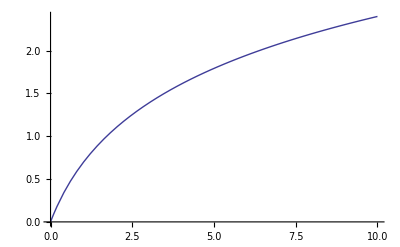

```mathematica
Plot[f[y],{y,0,10}]
```

## Using Functions

Note : Most of this applies to both pure functions and functions

### @ (Prefix)

```mathematica
Clear[f];
```

```mathematica
f@x
```

f[x]

```mathematica
(#^2&)@x
```

x^2

### @@ (Apply)

"f@@expr" Replaces “Head” of “expr” with f.

```mathematica
f@@Table[i,{i,1,5}]
```

f[1,2,3,4,5]

equivalently

```mathematica
Apply[f,Table[i,{i,1,5}]]
```

f[1,2,3,4,5]

```mathematica
(#1Plus[##2]&)@@Table[Subscript[x, i],{i,1,5}]
```

x_1 (x_2+x_3+x_4+x_5)

#### @@@

"f@@@list" Applies "f" on each element of “list” .

```mathematica
f@@@ Table[g[i],{i,1,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

equivalently

```mathematica
Apply[f,Table[g[i],{i,1,5}],{1}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
(#^2&)@@@ Table[g[i],{i,1,5}]
```

{1,4,9,16,25}

#### General levelspec

```mathematica
"Apply[f,table,{n}]" Applies "f" on each element of "list" of level "n" .
```

```mathematica
f@@Table[{i,j},{i,1,3},{j,1,3}]//MatrixForm
f@@@Table[{i,j},{i,1,3},{j,1,3}]//MatrixForm
Apply[f,Table[{i,j},{i,1,3},{j,1,3}],{2}]//MatrixForm
```

f[{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}}]

(f[{1,1},{1,2},{1,3}]
f[{2,1},{2,2},{2,3}]
f[{3,1},{3,2},{3,3}])

(f[1,1] | f[1,2] | f[1,3]
f[2,1] | f[2,2] | f[2,3]
f[3,1] | f[3,2] | f[3,3])

Beware

```mathematica
Apply[f,Table[{i,j},{i,1,3},{j,1,3}],2]//MatrixForm
```

(f[f[1,1],f[1,2],f[1,3]]
f[f[2,1],f[2,2],f[2,3]]
f[f[3,1],f[3,2],f[3,3]])

### Map

"f/@list" prefixes f to all elements of "list".

```mathematica
f/@Table[i,{i,1,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
(#^2&)/@Table[i,{i,1,5}]
```

{1,4,9,16,25}

"Map[f, table , {n}]"  prefixes f to level "n" elements of "table".

```mathematica
Map[f,Table[i j,{i,1,3},{j,1,3}],{2}]//MatrixForm
```

(f[1] | f[2] | f[3]
f[2] | f[4] | f[6]
f[3] | f[6] | f[9])

### MapAt

Allows mapping to specific elements of table (see help for syntax).

### MapIndexed

Same as map but supplies “f” with position in list as extra argument.

```mathematica
MapIndexed[f,Table[Subscript[x, i],{i,1,5}]]
```

{f[x_1,{1}],f[x_2,{2}],f[x_3,{3}],f[x_4,{4}],f[x_5,{5}]}

## Cool Applications

### (Differential) operators

```mathematica
Op[f_Function]:= Function[{x}, Derivative[1][f][x]+f[x]]
```

```mathematica
Op[(#^2&)][x]
```

2 x+x^2

```mathematica
Clear[f]
f[x_]:= x^2
Op[f]
```

Function[{x$},f'[x$]+f[x$]]

```mathematica
TeukolskyOperator[s_,l_,m_,a_,ω_,λ_]:=
Function[{f},Function[{r},Evaluate[1/(a^2+(-2+r) r)(a^2 m^2-2 ⅈ a m s+2 ⅈ a m r s-a^2 λ+2 r λ-r^2 λ-2 (a m (a^2+r^2)-ⅈ ((-3+r) r^2+a^2 (1+r)) s) ω+(a^2+r^2)^2 ω^2) f[r]+2 (-1+r) (1+s) f'[r]+(a^2+(-2+r) r) f''[r]]]]
```

```mathematica
TeukolskyOperator[-2,2,2,1/3,1/10,1][R][r]
```

1/(1/9+(-2+r) r)((1/3+(8 ⅈ)/3)+(2-(8 ⅈ)/3) r-r^2+1/100 (1/9+r^2)^2+1/5 (-2/3 (1/9+r^2)-2 ⅈ ((-3+r) r^2+(1+r)/9))) R[r]-2 (-1+r) R'[r]+(1/9+(-2+r) r) R''[r]

### Some notable functions that take (pure) functions as (optional) arguments.

Collect

```mathematica
Clear[f];
Sum[RandomInteger[10] x^RandomInteger[10] y^RandomInteger[10],{10}]
Collect[%,x,f]
```

x^2+3 x^2 y+10 x^3 y^2+8 x^7 y^6+x^9 y^7+2 x^2 y^8+3 x^2 y^9+5 y^10+x^5 y^10

x^3 f[10 y^2]+x^7 f[8 y^6]+x^9 f[y^7]+x^5 f[y^10]+f[5 y^10]+x^2 f[1+3 y+2 y^8+3 y^9]

ColorFunction (*option of Plot and related*)

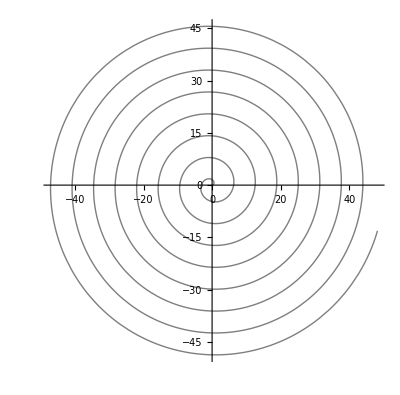

```mathematica
ParametricPlot[λ{Cos[λ],Sin[λ]},{λ,0,50},ColorFunction->Function[{x,y,λ},Hue[λ]]]
```

MeshFunctions (*option of Plot and related*)

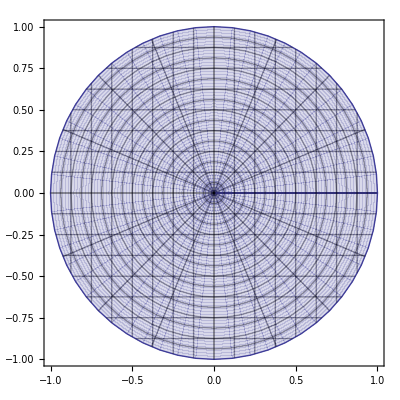

```mathematica
ParametricPlot[r{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},{r,0,1},
MeshFunctions->{
Function[{x,y,r,ϕ},x],
Function[{x,y,r,ϕ},y],
Function[{x,y,r,ϕ},r],
Function[{x,y,r,ϕ},ϕ]
}
]
```

RegionFunction (*option of ParametricPlot and related*)

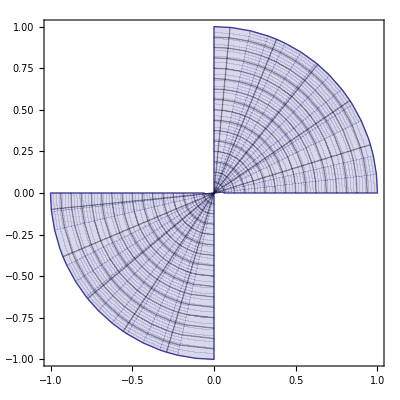

```mathematica
ParametricPlot[r{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},{r,0,1},
RegionFunction->Function[{x,y,r,ϕ},x y>0]
]
```